```mathematica
1)
```

```mathematica
clear[makePRG,m,M,k0,c];
makePRG[prgSymbol_,m1_,M1_,k01_,c1_]:=(
m[prgSymbol]^=m1;
M[prgSymbol]^=M1;
k0[prgSymbol]^=k01;
c[prgSymbol]^=c1;
);
clear[call];
call[prg_]:=(
k0[prg]^=Mod[(M[prg] k0[prg]+c[prg]),2^(m[prg])];
k0[prg]2^(-m[prg])
)
makePRG[prg1,40,5^9,1,0]
makePRG[prg2,31,65539,1,0]
N[Table[call[prg1],{10}]]
```

{1.77636×10^-6,0.469447,0.578034,0.442798,0.731522,0.178098,0.278709,0.810165,0.167068,0.700943}

```mathematica
2)
```

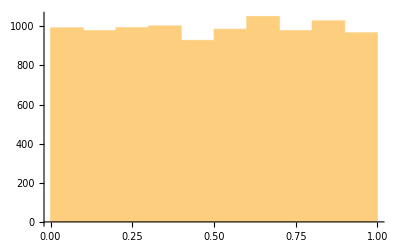

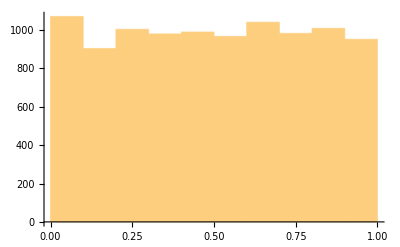

```mathematica
Histogram[N[Table[call[prg1],{n,100,10000}]],10]
Histogram[N[Table[call[prg2],{n,100,10000}]],10]
```

```mathematica
3)-4)
```

```mathematica
Clear testChi2;
testChi2[l_,m_,p_]:=(
n=Length[l];
y[k_]:=Length[Select[l,((#>(k/m)) && (#<((k+1)/m)))&]];
chi=Sum[(y[k]-(n/m))^2/(n/m),{k,0,m-1}];
{N[chi],InverseCDF[ChiSquareDistribution[m-1],p]}
)
testChi2[Table[call[prg1],{n,100,10000}],10,0.95]
testChi2[Table[call[prg2],{n,100,10000}],10,0.95]
```

{8.62832,16.919}

{24.8933,16.919}

```mathematica
5)
```

```mathematica
points1=Table[1,{333}];
points2=Table[1,{333}];
For[i =0,i<333,i++,points1[[i+1]]=Table[call[prg1],{999}][[{3i+1,3i+2,3i+3}]]];
For[i =0,i<333,i++,points2[[i+1]]=Table[call[prg2],{999}][[{3i+1,3i+2,3i+3}]]];
ListPlot3D[points1]
ListPlot3D[points2]
```

-Graphics3D-

-Graphics3D-

```mathematica
(*blujdanie*)
```

```mathematica
f[p_]:=2Floor[2 call[prg1]]-1+p    (*округление случайного числа 0-2, получаем 0 или 1, потом умножаем на 2, чтобы было 0 или 2, отнимаем 1*)
path[n_]:=NestList[f,0,n]
path[15]
```

{0,1,2,1,0,-1,0,1,0,1,2,1,2,3,2,1}

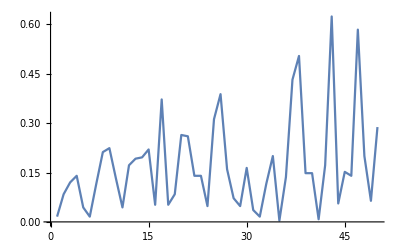

```mathematica
distAverage[nSteps_,nPaths_]:=Abs[Sum[path[nSteps][[nSteps+1]],{i,1,nPaths}]/nPaths]
ListPlot[Table[distAverage[ns,500],{ns,1,50}],Joined->True]
```

```mathematica
Fit[Table[distAverage[ns,1],{ns,0,1000}],{Sqrt[ns]},ns]
```

0.820049 √ns

```mathematica
0.82/Sqrt[2/π]
```

1.02772

```mathematica
distribution[nSteps_,nPaths_]:=Table[{i,Count[Table[path[nSteps][[nSteps+1]],{j,1,nPaths}],i]/nPaths},{i,-nSteps,nSteps}]  (*i,count[i] в таблице конечных точек*)
distribution[10,10]
```

{{-10,0},{-9,0},{-8,0},{-7,0},{-6,0},{-5,0},{-4,1/5},{-3,0},{-2,3/10},{-1,0},{0,1/5},{1,0},{2,1/5},{3,0},{4,0},{5,0},{6,0},{7,0},{8,0},{9,0},{10,0}}

```mathematica
distributionExact[ns_]:=(
n=Expand[((x+1/x)/2)^(ns)];
coefList=CoefficientList[n*x^ns,x];
Table[{j,coefList[[j+ns+1]]},{j,-ns,ns}]
)
distributionExact[3]
```

{{-3,1/8},{-2,0},{-1,3/8},{0,0},{1,3/8},{2,0},{3,1/8}}

```mathematica
N[distribution[3,10000]]
N[distributionExact[3]]
```

{{-3.,0.1183},{-2.,0.},{-1.,0.3761},{0.,0.},{1.,0.3761},{2.,0.},{3.,0.1228}}

{{-3.,0.125},{-2.,0.},{-1.,0.375},{0.,0.},{1.,0.375},{2.,0.},{3.,0.125}}